\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Introduction to Mathematica (MMA) -- 02

Zu-Cheng Chen

Institute of Theoretical Physics, 
Chinese Academy of Sciences

@ Guangzhou University, Jul 2019

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## List

## Create a list

### List

```mathematica
List[1,2,3,4,5]
```

{1,2,3,4,5}

```mathematica
a={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
a
```

{1,2,3,4,5}

```mathematica
?a
```

```mathematica
b={{x1,x2},{y1,y2}}
%//MatrixForm
```

{{x1,x2},{y1,y2}}

(x1 | x2
y1 | y2)

### Table

```mathematica
Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
c=Table[f[i]+f[j],{i,1,3},{j,1,3}]
c//MatrixForm
```

{{2 f[1],f[1]+f[2],f[1]+f[3]},{f[1]+f[2],2 f[2],f[2]+f[3]},{f[1]+f[3],f[2]+f[3],2 f[3]}}

(2 f[1] | f[1]+f[2] | f[1]+f[3]
f[1]+f[2] | 2 f[2] | f[2]+f[3]
f[1]+f[3] | f[2]+f[3] | 2 f[3])



```mathematica
Plot[Sin[x],{x,0,2π}]
```

```mathematica
Integrate[Sin[x],{x,0,2π}]
```

0

### Range

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[2,10]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Range[1,10,2]
```

{1,3,5,7,9}

## Access elements

```mathematica
c=Table[f[i]+f[j],{i, 1, 3},{j, 1, 3}]
```

{{2 f[1],f[1]+f[2],f[1]+f[3]},{f[1]+f[2],2 f[2],f[2]+f[3]},{f[1]+f[3],f[2]+f[3],2 f[3]}}

```mathematica
c[[1]]
```

{2 f[1],f[1]+f[2],f[1]+f[3]}

```mathematica
c[[1]][[2]]
```

f[1]+f[2]

```mathematica
c[[1,2]]
```

f[1]+f[2]

## +, -, *, /, ...

```mathematica
a=.
c=.
b=.
{a,b,c}+{x,y,z}
%+t
```

```mathematica
Plus[{a,b,c},{x,y,z}]
```

{a+x,b+y,c+z}

```mathematica
{a,b,c}-{x,y,z}
%-t
```

{a-x,b-y,c-z}

{a-t-x,b-t-y,c-t-z}

```mathematica
{a,b,c}*{x,y,z}
```

{a x,b y,c z}

```mathematica
{a,b,c}/{x,y,z}
```

{a/x,b/y,c/z}

```mathematica
{a,b,c}^p
```

{a^p,b^p,c^p}

```mathematica
Log[{a,b,c}]
```

{Log[a],Log[b],Log[c]}

```mathematica
Sin[{a,b,c}]
```

{Sin[a],Sin[b],Sin[c]}

## Attributes

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
Attributes[Minus]
```

{Listable,NumericFunction,Protected}

```mathematica
Attributes[Times]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected}

```mathematica
Attributes[Log]
```

{Listable,NumericFunction,Protected}

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

## Map == /@

```mathematica
Clear[a,b,c]
list={a,b,c}
f/@list
```

{a,b,c}

{f[a],f[b],f[c]}

```mathematica
Map[f,{a,b,c}]
f/@{a,b,c}
```

{f[a],f[b],f[c]}

{f[a],f[b],f[c]}

```mathematica
Sin[{a,b,c}]
```

```mathematica
f[{a,b,c}]
```

f[{a,b,c}]

```mathematica
Table[f[i],{i,{a,b,c}}]
```

{f[a],f[b],f[c]}

## Flatten

```mathematica
{a,b,{c,{{d1,d2},e},f}}//Flatten
```

{a,b,c,d1,d2,e,f}

```mathematica
{a,b,{c,{d,e},f}}
```

```mathematica
Flatten[{a,b,{c,{d,e},f}}]
```

{a,b,c,d,e,f}

## MemberQ

```mathematica
MemberQ[{a,b,{c,{d,e},f}},a]
```

True

```mathematica
MemberQ[{a,b,{c,{d,e},f}},d]
```

False

```mathematica
MemberQ[{a,b,{c,{d,e},f}},{c,{d,e},f}]
```

True

## Join

```mathematica
Join[{a,b,c},{x,y},{u,v,w}]
```

{a,b,c,x,y,u,v,w}

```mathematica
{a,b,c}~Join~{x,y}
```

{a,b,c,x,y}

```mathematica
{a,b,c}~Join~{x,y}~Join~{u,v,w}
```

{a,b,c,x,y,u,v,w}

```mathematica
{a,b,c}~Join~{x,y}
```

```mathematica
f[a]
f@a
a//f
```

f[a]

f[a]

f[a]

```mathematica
f[x,y]
x~f~y
```

f[x,y]

f[x,y]

## Dot

```mathematica
{
{a11,a12},
{a21,a22}
}//MatrixForm
```

(a11 | a12
a21 | a22)

```mathematica
{a,b,c} . {x,y,z}
```

a x+b y+c z

```mathematica
{{a,b},{c,d}}//MatrixForm
```

(a | b
c | d)

```mathematica
{{a,b},{c,d}} . {x, y}
```

{a x+b y,c x+d y}

```mathematica
{x,y} . {{a,b},{c,d}}
```

{a x+c y,b x+d y}

```mathematica
{{a,b},{c,d}}//MatrixForm
```

(a | b
c | d)

### Exercise

Calculate (8 | 4
3 | 5).(2 | 1
7 | 9)

```mathematica
({{8, 4}, {3, 5}}).({{2, 1}, {7, 9}})//MatrixForm
```

(44 | 44
41 | 48)

```mathematica
{{8,4},{3,5}}//MatrixForm
{{2,1},{7,9}}//MatrixForm
```

(8 | 4
3 | 5)

(2 | 1
7 | 9)

```mathematica
({{8, 4}, {3, 5}}).({{2, 1}, {7, 9}})//MatrixForm
```

(44 | 44
41 | 48)

```mathematica
{{8,4},{3,5}}.{{2,1},{7,9}}//MatrixForm
```

(44 | 44
41 | 48)

## Cross

```mathematica
Cross[{1,2,3},{1,1,1}]
```

{-1,2,-1}

```mathematica
x^2//TraditionalForm
```

x^2

## Norm

```mathematica
Norm[{a,b,c}]
```

√(Abs[a]^2+Abs[b]^2+Abs[c]^2)

```mathematica
Normalize[{a,b,c}]
```

{a/(√(Abs[a]^2+Abs[b]^2+Abs[c]^2)),b/(√(Abs[a]^2+Abs[b]^2+Abs[c]^2)),c/(√(Abs[a]^2+Abs[b]^2+Abs[c]^2))}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Everything in MMA is an expression!

## Head

```mathematica
a+b
```

```mathematica
c=Plus[a,b]
```

a+b

```mathematica
c=a+b
c//Head
```

a+b

Plus

```mathematica
Plus[a,b]
```

a+b

```mathematica
{a,b}
```

```mathematica
List[a,b]
```

```mathematica
c
```

a+b

```mathematica
c[[0]]
```

Plus

```mathematica
Plus[a,b]
```

```mathematica
c[[1]]
```

a

```mathematica
d=f[x+b[y],z*m]
```

f[x+b[y],m z]

```mathematica
d[[1]][[0]]
```

Plus

```mathematica
d[[1,0]]
```

Plus

```mathematica
d[[1]]
```

x+b[y]

## Replace head: @@

```mathematica
c=a+b
f@@c
```

a+b

f[a,b]

```mathematica
d={a,b}
f@@d
```

{a,b}

f[a,b]

## Map

```mathematica
Plus[x,y,z,u]
```

u+x+y+z

```mathematica
Plus[Log[x],Log@y,z//Log,Log@u]
```

Log[u]+Log[x]+Log[y]+Log[z]

```mathematica
expr=x+y+z+u
Log/@expr
```

u+x+y+z

Log[u]+Log[x]+Log[y]+Log[z]

## FullForm

```mathematica
a+b//FullForm
```

Plus[a,b]

```mathematica
d//FullForm
```

List[a,b]

## TreeForm

```mathematica
a+b^x//FullForm
```

Plus[a,Power[b,x]]

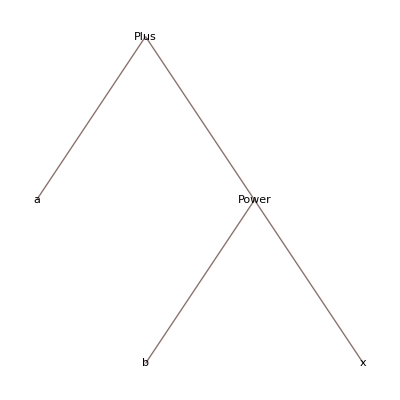

```mathematica
a+b^x//TreeForm
```

```mathematica
(a+b^x)[[2,2]]
```

x

## Exercise

Consider the following expression:
G[p,q][x,y,z]

How can you access the element q ?

```mathematica
expr=G[p,q][x,y,z]
```

G[p,q][x,y,z]

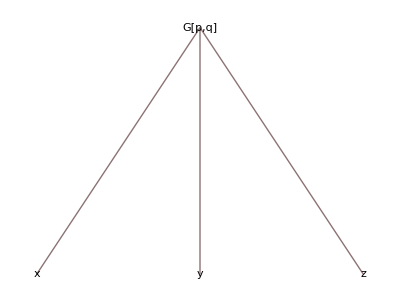

```mathematica
expr//TreeForm
```

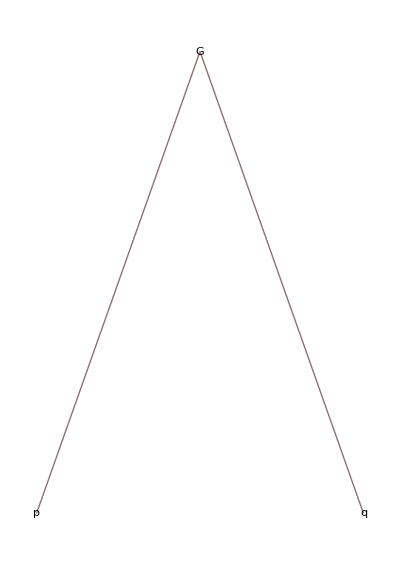

```mathematica
expr[[0]]//TreeForm
```

```mathematica
expr[[0,2]]
expr[[0,2]]//Head
```

q

Symbol

```mathematica
Symbol//Head
```

Symbol

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Rules

## _ : stands for any Wolfram Language expression

```mathematica
f[x_]:=x^2
```

```mathematica
f["a"]
```

a^2

```mathematica
("a")^2//FullForm
```

Power["a",2]

```mathematica
a^2
```

a^2

```mathematica
a^2//FullForm
```

Power[a,2]

```mathematica
Clear@f
rule01=f[x_]->x^2
```

f[x_]→x^2

```mathematica
f[3]
```

f[3]

```mathematica
f[3]/.rule01
```

9

```mathematica
f[3]/.f[x_]->x^2
```

9

```mathematica
rule02=f[x_]:>x^2
```

f[x_]:>x^2

```mathematica
f[3]/.rule02
```

9

```mathematica
x=5;
rule00=f[x_]->x^2
```

f[x_]→25

```mathematica
f[3]/.rule00
```

25

## __ : stands for any sequence of one or more Wolfram Language expressions

```mathematica
rule03=f[x__]:>Plus[x]
```

f[x__]:>+x

```mathematica
f[a,b]
```

f[a,b]

```mathematica
c=.
f[a,b,c]/.rule03
```

a+b+c

```mathematica
f[x__]:=Plus[x]
f[a,b]
```

a+b

## ___ : stands for any sequence of zero or more Wolfram Language expressions

```mathematica
Plus[]
```

0

```mathematica
Clear@f;
rule04=f[x___]:>Plus@x
```

f[x___]:>+x

```mathematica
f[a,b]
f[a,b]/.rule04
```

a+b

a+b

```mathematica
Clear@f
f[]
f[]/.rule04
```

f[]

0

```mathematica
{1,2,3}//Length
```

3

```mathematica
g[x___]:=Length[{x}]
g[1,2,3,4,5]
g[]
```

5

0

## ReplaceRepeated

```mathematica
Clear@f;
f[5]//.{f[1]->1,f[n_]->n f[n-1]}
```

120

```mathematica
f[5]/.{f[1]->1,f[n_]->n f[n-1]}
```

5 f[4]

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Pure function/Lambda function

```mathematica
f1[x_]:=x^2
```

```mathematica
f1[y]
```

y^2

```mathematica
f2=Function[x,x^2]
f2[y]
```

Function[x,x^2]

y^2

```mathematica
Function[y,y^2][3]
```

9

```mathematica
f3=Function[#^2]
f3[y]
```

#1^2&

y^2

```mathematica
2//(#^2&)
```

4

```mathematica
f4=#^2&
f4[y]
```

#1^2&

y^2

```mathematica
Sin[5]//N
```

-0.958924

```mathematica
N[Sin[5],10]
```

-0.9589242747

```mathematica
Sin[5]//N[#,10]&
```

-0.9589242747

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Module -- local variable

```mathematica
?f1
```

```mathematica
a=3;
g[x_]:=Module[
{a},
a=x^2+1;
Print[a]
]
```

```mathematica
g[3]
```

10

```mathematica
a
```

3

```mathematica
a=3;
g[x_]:=Module[
{},
a=x^2+1;
Print[a]
]
```

```mathematica
g[3]
```

10

```mathematica
a
```

10

## Exercise

Rewrite S_n function using Module.

```mathematica
α=3
```

3

```mathematica
Sn[f_]:=Module[
{L,mHz,POMS,Pacc,fStar,Sc,α,β,γ,κ,fκ,A},
L=2.5*10^9;
mHz=10^-3;POMS=(1.5*10^-11)^2*(1+(1/f 2*mHz)^4);
Pacc=(3*10^-15)^2*(1+((0.4*mHz)/f)^2)*(1+(f/(8*mHz))^4);
fStar=19.09*10^-3;
α=0.138;
β=-221;
κ=521;
γ=1680;
fκ=0.00113;
A=9*10^-45;
Sc=A*f^(-7/3)*ⅇ^(-f^α+β*f*Sin[κ*f])*(1+Tanh[γ*(fκ-f)]);

(10/(3*L^2))*(POMS+(4*Pacc)/(2*π*f)^4)*(1+(6/10)*(f/fStar)^2)+Sc
]
```

```mathematica
Sn[0.1]
```

2.14823×10^-39

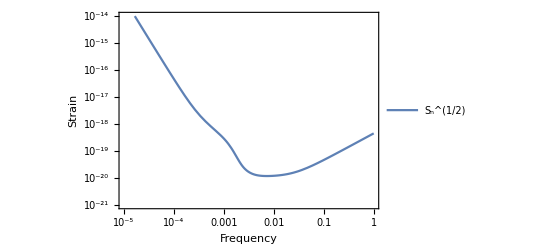

```mathematica
LogLogPlot[{Sn[f]^(1/2)},{f,10^-5,1},Frame->True,FrameLabel->{"Frequency","Strain"},PlotRange->{{10^-5,10^0},{10^-21,10^-14}},PlotLegends->{"S_n^(1/2)"}]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Options

```mathematica
Options[Plot]//Column
```

AlignmentPoint→Center
AspectRatio→1/GoldenRatio
Axes→True
AxesLabel→None
AxesOrigin→Automatic
AxesStyle→{}
Background→None
BaselinePosition→Automatic
BaseStyle→{}
ClippingStyle→None
ColorFunction→Automatic
ColorFunctionScaling→True
ColorOutput→Automatic
ContentSelectable→Automatic
CoordinatesToolOptions→Automatic
DisplayFunction:>$DisplayFunction
Epilog→{}
Evaluated→Automatic
EvaluationMonitor→None
Exclusions→Automatic
ExclusionsStyle→None
Filling→None
FillingStyle→Automatic
FormatType:>TraditionalForm
Frame→False
FrameLabel→None
FrameStyle→{}
FrameTicks→Automatic
FrameTicksStyle→{}
GridLines→None
GridLinesStyle→{}
ImageMargins→0.
ImagePadding→All
ImageSize→Automatic
ImageSizeRaw→Automatic
LabelingSize→Automatic
LabelStyle→{}
MaxRecursion→Automatic
Mesh→None
MeshFunctions→{#1&}
MeshShading→None
MeshStyle→Automatic
Method→Automatic
PerformanceGoal:>$PerformanceGoal
PlotLabel→None
PlotLabels→None
PlotLegends→None
PlotPoints→Automatic
PlotRange→{Full,Automatic}
PlotRangeClipping→True
PlotRangePadding→Automatic
PlotRegion→Automatic
PlotStyle→Automatic
PlotTheme:>$PlotTheme
PreserveImageOptions→Automatic
Prolog→{}
RegionFunction→(True&)
RotateLabel→True
ScalingFunctions→None
TargetUnits→Automatic
Ticks→Automatic
TicksStyle→{}
WorkingPrecision→MachinePrecision

## Attributes

```mathematica
x=.
Sqrt[x^2]
```

√(x^2)

```mathematica
Sqrt[x_^2]:=x
```

SetDelayed::write: Tag Sqrt in √(x_^2) is Protected.

$Failed

```mathematica
Attributes[Sqrt]
```

{Listable,NumericFunction,Protected}

```mathematica
Unprotect[Sqrt];
```

```mathematica
Sqrt[x_^2]:=x
```

```mathematica
Sqrt[x^2]
```

x

```mathematica
Protect[Sqrt]
```

{Sqrt}

```mathematica
Sqrt[x_^2]:=x
```

SetDelayed::write: Tag Sqrt in √(x_^2) is Protected.

$Failed

```mathematica
f[x_]:=Sin[x^2+2]
```

```mathematica
SetAttributes[f,Protected]
```

```mathematica
f[x_]:=Sin[x^2]
```

SetDelayed::write: Tag f in f[x_] is Protected.

$Failed

```mathematica
Clear@f
```

Clear::wrsym: Symbol f is Protected.

```mathematica
Remove[f]
```

Remove::rmptc: Symbol f is Protected and cannot be removed.

```mathematica
Unprotect[f]
```

{f}

```mathematica
Clear[f]
```

```mathematica
?f
```

## Default values

```mathematica
h[x_:2,y_:3]:=x/y
```

```mathematica
h[]
```

2/3

```mathematica
h[1]
```

1/3

## Default options

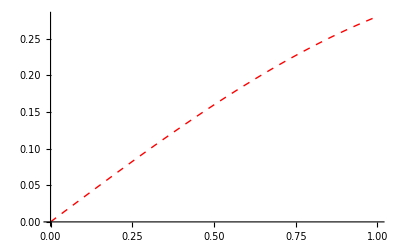

```mathematica
myPlot[xexper_,OptionsPattern[{opp1->3,plotstyle->Directive[Red,Thick,Dashed]}]]:=Plot[xexper/OptionValue[opp1],{x,0,1},PlotStyle->OptionValue[plotstyle]]

myPlot[Sin[x]]
```

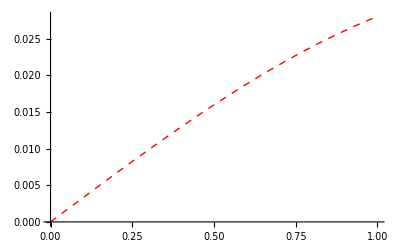

```mathematica
myPlot[Sin[x],opp1->30]
```

## Usage informations

```mathematica
test[x_]:=x^2
test::usage="This is a test function";
```

```mathematica
test[3]
```

9

```mathematica
?Sin
```

```mathematica
?test
```

```mathematica
??test
```

## Compile

```mathematica
f=Function[{x,n},Sin[x]+x^n];
```

```mathematica
cf= Compile[{{x, _Real},{n,_Integer}}, Sin[x] + x^n,Parallelization->True];
```

```mathematica
Timing[Do[f[1.0,2],{10^6}]]
```

{1.47417,Null}

```mathematica
Timing[Do[cf[1.0,2],{10^6}]]
```

{0.392337,Null}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Visualization

## Plot

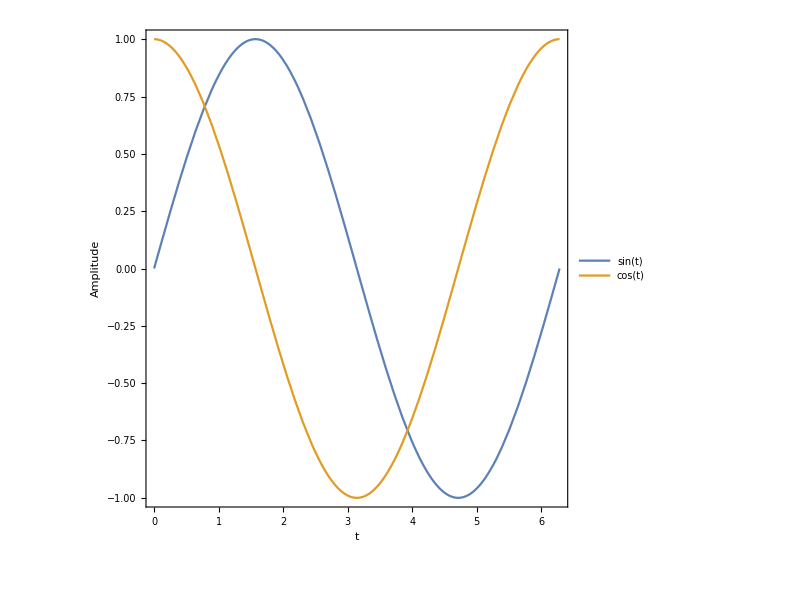

```mathematica
Plot[{Sin[t],Cos[t]},{t,0,2*π},Frame->True,PlotLegends->"Expressions",FrameLabel->{"t","Amplitude"},BaseStyle->Large,ImageSize->600,AspectRatio->1]
```

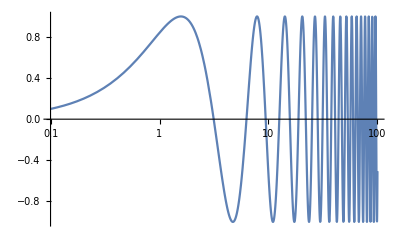

```mathematica
LogLinearPlot[Sin[x],{x,10^-1,10^2},PlotRange->All]
```

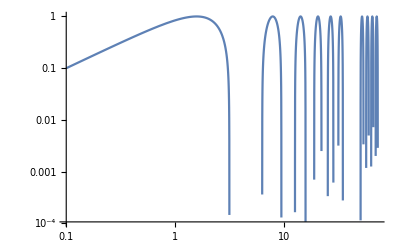

```mathematica
LogLogPlot[Sin[x],{x,10^-1,10^2},PlotRange->All]
```

```mathematica
Plot3D[Sin[x]*Cos[y],{x,0,2*π},{y,0,2*π},AxesLabel->Automatic]
```

-Graphics3D-

## ListPlot

```mathematica
data=Table[{x,Sin[x]},{x,0,2*π,0.1}];
```

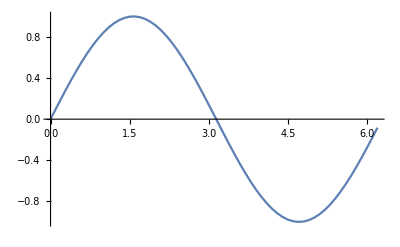

```mathematica
ListPlot[data,Joined->True]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Parallel

```mathematica
Clear@f;
f[x_?NumericQ]:=NIntegrate[x*Sin[y+x]*Cos[y],{y,1,10}]
```

```mathematica
f[1]//AbsoluteTiming
```

{0.009393,3.67605}

```mathematica
xs=Range[2*10^3];
```

```mathematica
f/@xs;//AbsoluteTiming
```

{13.1428,Null}

```mathematica
Map[f,xs];//AbsoluteTiming
```

{13.5662,Null}

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
Distribute@f;
```

```mathematica
(ParallelMap[f,xs]);//AbsoluteTiming
```

{3.45669,Null}

```mathematica
(data=ParallelTable[{x,f[x]},{x,xs}];)//AbsoluteTiming
```

{3.10925,Null}

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Import/Export

Create a "backup" directory

```mathematica
NotebookDirectory[]
```

/home/bear/projects/working/Mathematica_Tutorials/day2/

```mathematica
Directory[]
```

/home/bear

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bear/projects/working/Mathematica_Tutorials/day2

```mathematica
Directory[]
```

/home/bear/projects/working/Mathematica_Tutorials/day2

```mathematica
SetDirectory[NotebookDirectory[]];

If[
Not[DirectoryQ["backup"]],CreateDirectory["backup"]
];
```

```mathematica
Export["backup/data.m",data]
```

backup/data.m

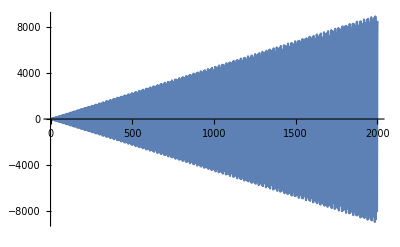

```mathematica
data=Import["backup/data.m"];
ListPlot[data,Joined->True]
```

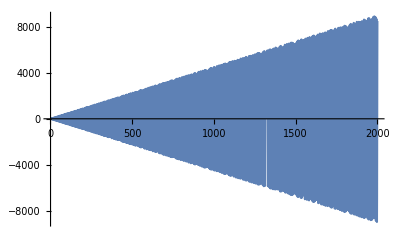
{20.7117,-Graphics-}

```mathematica
Plot[f[x],{x,1,2000}]//AbsoluteTiming
```